# 38: Conjugate Gradients (CG)

We saw that Arnoldi and all sorts of other stuff became simpler for symmetric matrices. In particular, we could build a expanding orthogonal basis for the Krylov space  	
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b})
without orthogonalizing against all the previous directions.  The simplified process to build the tridiagonal H and the orthogonal Q was renamed the Lanczos process. Code to iteratively compute the diagonal α and subdiagonal β entries of H and the orthogonal Q is below.

A very specific simplification is possible when solving A.x=b and A is Symmetric a positive definite.  It is the original Krylov space solver and is very effective when applicable and appropriately preconditioned.

## Lanczos Code

```mathematica
LanczosInit[A_][q1_]:= Module[{v,α1,β1,q2},
v=A.q1;
α1=q1.v;
v = v - α1 q1;
β1=Norm[v];
q2=v/β1;
{{q1,q2}ᵀ,{{α1},{β1}}}
]
Lanczos[A_][{Q_,{α_,β_}}]:= Module[{m,n,qn,v,αn,βn,qNew},
{m,n}=Dimensions[Q];
qn=Q⟦All,n⟧;
v=A.qn;
αn=qn.v;
v=v-β⟦n-1⟧ Q⟦All,n-1⟧-αn qn;
βn=Norm[v];
qNew=v/βn;
{ArrayFlatten[({{Q, {qNew}ᵀ}})],{Append[α,αn],Append[β,βn]}}
]
```

Testing.  Note the preliminary initialization!

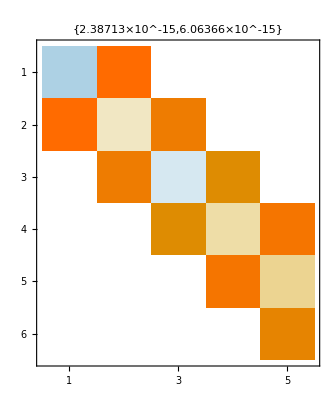

```mathematica
m=123;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
q1=Normalize[RandomReal[{-1,1},m]];
{Q1,{α1,β1}}=LanczosInit[A][q1];
n=5;
{Q,{α,β}}=Nest[Lanczos[A],{Q1,{α1,β1}},n-1];
H=SparseArray[{Band[{1,1}]->α,Band[{2,1}]->β,Band[{1,2}]->Drop[β,-1]}];
MatrixPlot[H,
PlotLabel->Map[Norm,{Qᵀ.Q-IdentityMatrix[n+1],A.Q⟦All,1;;n⟧-Q.H}]]
```

## Solving A.x=b with Conjugate Gradients.

From now on we are going to assume that A ϵ ℝ^(m×m) is Symmetric and Positive Definite abbreviated to SPD and write x_∞ for the solution satisfying A.x_∞=b.  As a reminder positive definite means x.A.x>0 unless x=0.  As a result SPD means ||x(||)_(CG(A)):=√(x.A.x) is a norm!   Minimizing the residual using this specially tailored norm gives the very simple and effective conjugate gradient algorithm.

### Residual Computation and Cost Function ϕ.

The first thing to do is to work out what is special about this way of measuring the residual.  Take a look
  	||x-x_∞(||)_(CG(A))^2=(x-x_∞).A.(x-x_∞)=(x-x_∞).(A.x-A.x_∞)=(x-x_∞).(A.x-b)=x.A.x-x.b-x_∞.A.x+x_∞.b
  Maybe nothing stand out right now but remember A=Aᵀ so x_∞.A.x=(Aᵀ.x_∞).x=(A.x_∞).x=b.x so 
  	||x-x_∞(||)_(CG(A))^2=x.A.x-x.b-x_∞.A.x+x_∞.b=x.A.x-2 x.b+x_∞.b=2(1/2 x.A.x - b.x)+constant.
  Define
  	ϕ(x)=1/2 x.A.x - b.x
 and note that the readily computable derivative
  	Dϕ(x)=A.x - b=-(b-A.x)=-r(x)
is just the negative of residual.  In words, we can solve A.x=b by minimizing ϕ. In symbols, 	
	x_∞=argmin ϕ(x).

### Line Search

One way to minimize a convex function is to head downhill from any starting point until you hit bottom (in that direction) then turn to a new downhill direction and repeat the process until you get to the overall minimum.  We are going to write p_n for the search direction.  Straight downhill from a point x_n is
	-Dϕ(x_n)=b-A.x_n=r_n.  
which is just the residual r_n=b-A.x_n.  Any direction p_n with p_n.r_n>0 is downhill.

Along any downhill search direction p_n we have a single variable quadratic in α 
	g(α):=ϕ(x_n+α p_n)=1/2(x_n+α p_n).A.(x_n+α p_n)-b.(x_n+α p_n)
with derivative
	g'(α)=(x_n+α p_n).A.p_n-b.p_n=(A.x_n-b).p_n+α p_n.A.p_n=α p_n.A.p_n-p_n.p_n.
Solve g'(α)=0 give the minimum at 
	α_(n+1)=p_n.p_n/(p_n.A.p_n)
which defines our improved approximate solution
	x_(n+1)=x_n+α_n p_n.
If r(x_(n+1))=-Dϕ(x_(n+1))=0 then x_(n+1) is the global minimum. If  r(x_(n+1))≠0 we can continue the iterative process to further reduce ϕ(x).

A direct computation explicitly gives the explicit formula for the improvement 
	ϕ(x_n)-ϕ(x_(n+1))=1/2(p_n.p_n)^2/(p_n.A.p_n).
Not surprisingly the update conditions have geometric interpretations.  Since p_n is tangent to the ϕ contour at x_(n+1) we have p_n⊥r_(n+1). Since α_(n+1)is determined by setting
	g'(α)=α p_n.A.p_n-p_n.p_n=-p_n.(p_n-α A.p_n)
to zero and solving for α_(n+1) we have p_n⊥(p_n-α_(n+1) A.p_n).

If p_n=r_n this is a steepest descent method for ϕ(x) with an "exact" line search: Steepest descent because it searches along the negative gradient -Dϕ(x_n); Exact line search because α_n gives the exact minimum along the search (steepest descent) direction.

A direct computation explicitly gives the explicit formula for the improvement 
	ϕ(x_n)-ϕ(x_(n+1))=1/2(r_n.r_n)^2/(r_n.A.r_n).
Not surprisingly the update conditions have geometric interpretations.  Since r_n is tangent to the ϕ contour at x_(n+1) we have r_n⊥r_(n+1). The g'(α_(n+1))=0 condition can be interpreted as r_n⊥(r_n-α_(n+1) A.r_n)
	g'(α)=α r_n.A.r_n-r_n.r_n=-r_n.(r_n-α A.r_n).

At this point there is a lot of freedom in choosing the search direction p_n.  The method is guaranteed to converge provided r_n.p_n>0. Unfortunately, the obvious choice p_n=r_n zig-zags and can be very slow. The choice in the algorithm is basically the choice made in the Lanczos orthogonalization which ensures that in exact arithmetic the algorithm produces the minimum over the Krylov space.

### Algorithm 38.1

Conjugate gradients (Algorithm 38.1) is simply this exact line search minimization starting from the predetermined  initial guess x_0=OverVector[0].  Here is the pseudo code from the text

Conjugate Gradients
x_0=0, r_0=b, p_0=r_0
for n in 1, 2, 3, ...
	α_n=(r_(n-1).r_(n-1))/(p_(n-1).A.p_(n-1))
	x_n=x_(n-1)+α_n p_(n-1)
	r_n=r_(n-1)-α_n A.p_(n-1)
	β_n=(r_n.r_n)/(r_(n-1).r_(n-1))
	p_n=r_n+β_n p_(n-1)

Lets look at the start of this process in 2D.

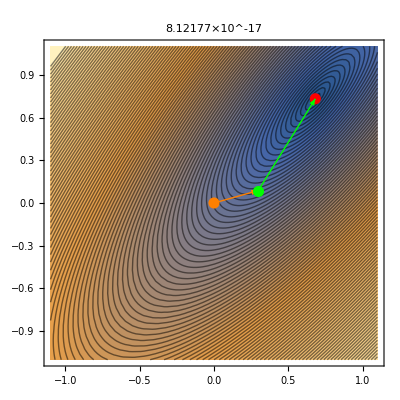

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ; 
CGNorm[A_][x_]:=√(x.A.x)
xInf= Normalize[RandomReal[{-1,1},m]];
(* Initialization *)
b=A.xInf;
r0 =b;p0=r0;x0=0*b;
(* n=1 *)
α1 = (r0.r0)/(p0.A.p0);
x1 =x0 + α1 p0;
r1=r0-α1 A.p0;
β1 = (r1.r1)/(r0.r0);
p1=r1 + β1 p0;
(* n=2 just the start *)
α2 = (r1.r1)/(p1.A.p1);
x2 =x1 + α2 p1;
r2=r1-α2 A.p1;
(* Pic *)
ContourPlot[CGNorm[A][{x,y}-xInf],
{x,-1.1,1.1},
{y,-1.1,1.1},
Contours->100,
AspectRatio->Automatic,
Epilog->{PointSize[0.02],
{Red,Point[xInf]},
{Orange, Point[x0], Arrow[{x0,x1}]},
{Green, Point[x1], Arrow[{x1,x2}]}
},
PlotLabel->Norm[r2]
]
```

Lets try to look at the start of this process in 3D.

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];A=A.Aᵀ; 
CGNorm[A_][x_]:=√(x.A.x)
xInf= Normalize[RandomReal[{-1,1},m]];
(* Initialization *)
b=A.xInf;
r0 =b;p0=r0;x0=0*b;
(* n=1 *)
α1 = (r0.r0)/(p0.A.p0);
x1 =x0 + α1 p0;
r1=r0-α1 A.p0;
β1 = (r1.r1)/(r0.r0);
p1=r1 + β1 p0;
(* n=2 just the start *)
α2 = (r1.r1)/(p1.A.p1);
x2 =x1 + α2 p1;
r2=r1-α2 A.p1;
(* Pic *)
ϕVals=Map[CGNorm[A],{x0-xInf,x1-xInf,x2-xInf}]
Show[
ContourPlot3D[CGNorm[A][{x,y,z}-xInf],
{x,-1.1,1.1},
{y,-1.1,1.1},
{z,-1.1,1.1},
ContourStyle->Opacity[0.5],
Contours->ϕVals,
AspectRatio->Automatic,
PlotLabel->Norm[r2]
],
Graphics3D[{PointSize[0.02],
{Red,Point[xInf]},
{Orange,Point[x0],Arrow[{x0,x1}]},
{Green,Point[x1],Arrow[{x1,x2}]}}]]
```

{1.29149,0.213182,0.12597}

-Graphics3D-

### CG Code

A single step directly (the only modification is to store the matrix vector multiplication) from pseudo code.

```mathematica
CGStep[A_][{xIn_,rIn_,pIn_}]:=Module[{ApIn=A.pIn,α,β,xOut,rOut,pOut},
α=(rIn.rIn)/(pIn.ApIn);
xOut=xIn+α pIn;
rOut=rIn - α ApIn;
β = (rOut.rOut)/(rIn.rIn); 
pOut=rOut+β pIn;
{xOut,rOut,pOut}]
```

Note, essentially all the work per step is the matrix vector-multiplication.  Find the thing that could be made more efficient! Tell me why I do not care very much!

Import an SPD A 
	https://math.nist.gov/MatrixMarket/data/Harwell-Boeing/bcsstruc1/bcsstk05.html
from Matrix Market.

```mathematica
A=Import["https://math.nist.gov/pub/MatrixMarket2/Harwell-Boeing/bcsstruc1/bcsstk05.mtx.gz"];
(*MatrixPlot[A]*)
m=Length[A];
MaxIter=50;
(* Create an identifiable RHS *)
xInf=Table[Cos[0.1 i],{i,m}];
ListPlot[xInf];
b=A.xInf;
{x0,r0,p0}={0*b, b,b};
xrpData=NestList[CGStep[A],{x0,r0,p0},MaxIter];
TabView[{
"x"->MatrixPlot[xrpData⟦All,1⟧],
"r"->MatrixPlot[xrpData⟦All,2⟧],
"p"-> MatrixPlot[xrpData⟦All,3⟧]
}]
TabView[{
"||x-x_∞(||)_(CG (A))"->ListLogPlot[Map[CGNorm[A][#-xInf]&,xrpData⟦All,1⟧]],
"||x-x_∞(||)_2"->ListLogPlot[Map[Norm[#-xInf]&,xrpData⟦All,1⟧]],
"||r||"->ListLogPlot[Map[Norm,xrpData⟦All,2⟧]]
}]
```

123

123

Slow but very steady is what I would say here. Remember, preconditioners are essential!

```mathematica
MatrixPlot[A,PlotLegends->Automatic]
```

-Graphics-

## Convergence

We already know from either the derivation or the code that

The CG norm of the residual ||x_n-x_∞(||)_(CG(A))^2=(x_n-x_∞).A.(x_n-x_∞)=2ϕ(x_n)+constant.

We also know know from either the derivation or the code that

r_(n+1).r_n=0

p_(n+1).A.p_n=0

and an induction argument shows that as longs the computation does not converge i.e. r_n=0

Residuals r_n are orthogonal i.e. r_j.r_n=0 for j<n

Search directions p_n are A conjugate i.e. p_j.A.p_n=0 for j<n

We can reinterpret this in terms of the Krylov Space
	𝒦_n=span{x_1,x_2,…,x_n}=span{p_1,p_2,…,p_n}=span{r_0,r_1,…,r_(n-1)}
which are all equal to the standard Krylov space
	𝒦_n(b,A)=span{b,A.b,…,A^(n-1).b}

Theorem 38.2 says in part that in exact arithmetic the CG algorithm converges monotonically in the CG norm and terminates in n steps with n≤m. This is not surprising! We have seen the monotonicity, it runs out of dimensions to search after m steps, and the only thing that can go wrong r_k=0 would indicate convergence.

The more useful part of Theorem 38 says that x_n minimizes x_n=argmin_𝒦_n||x-x_∞(||)_(CG(A)).  To see this plug x=x_n+Δx∈𝒦_n into the tailored norm and expand to get 
	||x-x_∞(||)_(CG(A))^2=(x_n-x_∞+Δx).A.(x_n-x_∞+Δx)=(x_n-x_∞).A.(x_n-x_∞)+Δx.A.Δx+2(x_n-x_∞).A.Δx
The conjugacy built into the algorithm ensures the last term is zero so 
	||x-x_∞(||)_(CG(A))^2=(x_n-x_∞+Δx).A.(x_n-x_∞+Δx)=(x_n-x_∞).A.(x_n-x_∞)+Δx.A.Δx≥(x_n-x_∞).A.(x_n-x_∞)
Since A is SPD and the last term is strictly positive unless Δx=0

In floating point arithmetic the algorithm can stall i.e. stop making useful progress. In practice, like all other iterative algorithms CG really needs preconditioned.

## Optimality and Convergence

Just like the other Krylov algorithms we have looked at CG has an optimality property for polynomials.  Not surprisingly CG is optimal in the tailored norm. Theorem 38.3 shows that CG constructs the polynomial that minimizes ||p_n(A)(x_∞-x_0)(||)_(CG(A)) over the set of polynomials with p(0)=1 where our initial guess x_0is always the zero vector. The trick to seeing this is to use the orthogonal eigen basis {v_1,v_2,…,v_m} for A and note that 
	||p(A)(x_∞-x_0)(||)_(CG(A))^2=∑_(j=1)^m a_j^2 λ_j * (p(λ_j))^2 and ||(x_∞-x_0)(||)_(CG(A))^2=∑_(j=1)^m a_j^2 λ_j
where x_∞-x_0=∑_(j=1)^m a_j v_j.  Just like before we get a useful expression for the appropriate scaled relative error
	(||x_∞-x_n(||)_(CG(A)))/(||x_∞-x_0(||)_(CG(A)))=minp∈𝒫_n (||p(A)(x_∞-x_0)(||)_(CG(A)))/(||x_∞-x_0(||)_(CG(A)))≤minp∈𝒫_n max_(λ∈Λ(A))|p(λ)|.

This has lots of useful consequences for matrices with clustered eigenvalues. The book presents two very different results.

The first theorem is a positive theorem which concerns  eigenvalues clustered as tightly as possible in the sense that there are only n "distinct" eigenvalues: the theorem says that CG converges in less than n-steps. The reason this is plausible is that a single CG step simultaneously resolves all directions in a scalar multiple of the identity. In practice, CG resolves tight clusters of eigenvalues almost simultaneously.  In practice, the theorem says that convergence is fast for matrices with a few “tight” eigenvalue clusters.

The second theorem is a worst case theorem which gives the slowest possible convergence rate for a spectrum with eigenvalues λ spread between 0<λ_min≤λ≤λ_max in terms of the condition number κ=λ_max/λ_min. The theorem is expressed as 
	 (||x_∞-x_n(||)_(CG(A)))/(||x_∞-x_0(||)_(CG(A)))≤2((√κ-1)/(√κ+1))^n∼(1-2/(√k))^n

### Clustered Examples

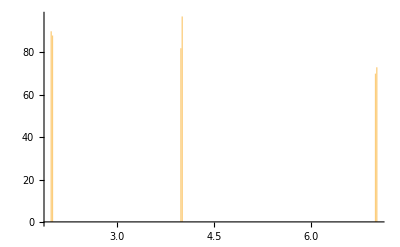

```mathematica
m=500;
ϵ=10^-6;
dist=MixtureDistribution[{1,1,1},
{NormalDistribution[2,ϵ],NormalDistribution[4,2ϵ],NormalDistribution[7,3ϵ]}];
λs=RandomVariate[dist,m];
Q=Orthogonalize[RandomReal[{-1,1},{m,m}]];
A=Q.DiagonalMatrix[λs].Qᵀ;
Histogram[λs,200]
```

```mathematica
xInf=RandomReal[{-1,1},m];
b=A.xInf;
MaxIter=8;
{x0,r0,p0}={0*b, b,b};
xrpData=NestList[CGStep[A],{x0,r0,p0},MaxIter];
TabView[{
"x"->MatrixPlot[xrpData⟦All,1⟧],
"r"->MatrixPlot[xrpData⟦All,2⟧],
"p"-> MatrixPlot[xrpData⟦All,3⟧]
}]
TabView[{
"||x-x_∞(||)_(CG (A))"->ListLogPlot[Map[CGNorm[A][#-xInf]&,xrpData⟦All,1⟧]],
"||x-x_∞(||)_2"->ListLogPlot[Map[Norm[#-xInf]&,xrpData⟦All,1⟧]],
"||r||"->ListLogPlot[Map[Norm,xrpData⟦All,2⟧]]
}]
```

123

123

### Non-Clustered Examples

0.980198

700

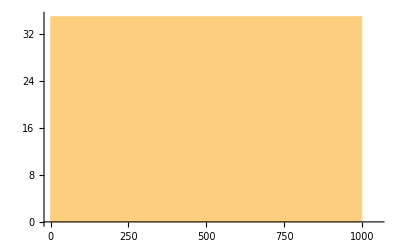

```mathematica
m=700;
{λMin,λMax}={0.1,1000};
κEst=λMax/λMin;
EstRate=(√κEst-1)/(√κEst+1)
λs=Table[λ,{λ,λMin,λMax,(λMax-λMin)/(m-1)}];
Length[λs]
Q=Orthogonalize[RandomReal[{-1,1},{m,m}]];
A=Q.DiagonalMatrix[λs].Qᵀ;
Histogram[λs,25]
```

```mathematica
xInf=RandomReal[{-1,1},m];
b=A.xInf;
MaxIter=100;
{x0,r0,p0}={0*b, b,b};
xrpData=NestList[CGStep[A],{x0,r0,p0},MaxIter];
TabView[{
"x"->MatrixPlot[xrpData⟦All,1⟧],
"r"->MatrixPlot[xrpData⟦All,2⟧],
"p"-> MatrixPlot[xrpData⟦All,3⟧]
}]
TabView[{
"||x-x_∞(||)_(CG (A))"->ListLogPlot[{
Map[CGNorm[A][#-xInf]&,xrpData⟦All,1⟧],
Table[EstRate^n,{n,1,MaxIter}]}],
"||x-x_∞(||)_2"->ListLogPlot[Map[Norm[#-xInf]&,xrpData⟦All,1⟧]],
"||r||"->ListLogPlot[Map[Norm,xrpData⟦All,2⟧]]
}]
```

123

123